```mathematica
Nt = 551; (*1000 -> default*)(*10 -> simple case to compare to reduced points*)
ti = 0; tf = 1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*500 default from problem*)(*200 -> my choice*) (*25 -> simple case to compare to reduced points*)
xi = 0; xf = 2*Pi; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax);

(*For Eigenvalue Plots in Complex Plane*)
(*rs = {0.9,1,1.1};*)
(*rs = {1.4,1.5,1.6};*)(*When exporting RK4 and LD4*)

(*For Max Eigenvalue Plots*)
rs = Table[0.01*i,{i,1,10}];

PSfinalerrorCN = Table[0,{i,1,Length[rs]}];
PSfinalerrorEuler = Table[0,{i,1,Length[rs]}];
PSfinalerrorRK2 = Table[0,{i,1,Length[rs]}];
PSfinalerrorRK4 = Table[0,{i,1,Length[rs]}];
PSfinalerrorLD4 = Table[0,{i,1,Length[rs]}];

f[x_] =ⅇ^(- 8(x-π)^2);
```

```mathematica
Dimensions[MN]
```

{551,551}

```mathematica
Do[
deltat = deltax * rs[[p]];

h = (2*Pi)/ (Nx);

T = Table[tn = ti + n *deltat, {n, 0, Nt -1 }];
Xo = Table[xn = xi + n *deltax, {n, 0, Nx -1}];

X = (Xo-xi)*((2*Pi))/(xf-xi);


D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}]];
(*D1 = N[D1,32];*)
D2 = MatrixPower[D1,2];
DL = -c * D1 * deltat;


(* Crank-Nicolson *)
UCN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UCN[[1,All]] = f[X];
UCN = N[UCN];
UCN = Chop[N[UCN], 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN];


I1 = IdentityMatrix[Length[D1]];
I1 = N[I1];
A = I1 - ((DL / 2));
A = N[A];
B = I1 + ((DL / 2));
B = N[B];
MCN = Inverse[A].B;
EMCN = MCN - I1;

Do[UCN[[n+1,All]] = UCN[[n,All]] + (EMCN ).UCN[[n,All]], {n,1,Nt - 1 }];

FCN = Table[0,{i,1,Nt},{j,1,Nx}];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
Do[
FCN[[i]] = (D1.UCN[[i,All]])^2;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];

PSfinalerrorCN[[p]] =Abs[Last[intCN] - intCN[[1]]]; 



(*RK2*)
URK2= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK2[[1,All]] = f[X];
URK2 = N[URK2];
URK2 = Chop[N[URK2], 10^(-307)];
URK2 = Developer`ToPackedArray[URK2, Real]; 
Developer`PackedArrayQ[URK2];

IRK2 = IdentityMatrix[Length[DL]];
IRK2 = N[IRK2];

MRK2 = (IRK2 + (DL) + ((1/2)*(MatrixPower[DL,2])));

EMRK2 = MRK2 - IRK2;

Do[URK2[[n+1,All]] = URK2[[n,All]] + (EMRK2).URK2[[n,All]], {n,1,Nt - 1 }];

FRK2= Table[0,{i,1,Nt},{j,1,Nx}];
intRK2 = Table[0,{i,1,Length[FRK2[[All,1]]]}];
Do[
FRK2[[i]] = (D1.URK2[[i,All]])^2;

intRK2[[i]] = (2π)/Nx Total[FRK2[[i,All]]]
,{i,1,Length[FRK2[[All,1]]]}];

PSfinalerrorRK2[[p]] =Abs[Last[intRK2] - intRK2[[1]]];

(*RK4*)
URK4= Table[0, {n, 1, Nt}, {m, 1, Nx }];
URK4[[1,All]] = f[X];
URK4 = N[URK4];
URK4 = Chop[N[URK4], 10^(-307)];
URK4 = Developer`ToPackedArray[URK4, Real]; 
Developer`PackedArrayQ[URK4];

IRK4 = IdentityMatrix[Length[DL]];
IRK4 = N[IRK4];

MRK4 = IRK4 + DL + ((1/2) * (MatrixPower[DL,2])) + ((1/6) * (MatrixPower[DL,3])) + ((1/24) * (MatrixPower[DL,4]));

EMRK4 = MRK4 - IRK4;

Do[URK4[[n+1,All]] = URK4[[n,All]] + (EMRK4).URK4[[n,All]], {n,1,Nt - 1 }];

FRK4= Table[0,{i,1,Nt},{j,1,Nx}];
intRK4 = Table[0,{i,1,Length[FRK4[[All,1]]]}];
Do[
FRK4[[i]] = (D1.URK4[[i,All]])^2;

intRK4[[i]] = (2π)/Nx Total[FRK4[[i,All]]]
,{i,1,Length[FRK4[[All,1]]]}];

PSfinalerrorRK4[[p]] =Abs[Last[intRK4] - intRK4[[1]]];

(*LD4*)
UN= Table[0, {n, 1, Nt}, {m, 1, Nx }];
UN[[1,All]] = f[X];
UN = N[UN];
UN = Chop[N[UN], 10^(-307)];
UN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UN];


IN = IdentityMatrix[Length[D1]];
IN = N[IN];
AN = IN - ((DL / 2)) + (((MatrixPower[DL,2])/12));
AN = N[AN];
BN = IN + ((DL / 2)) + (((MatrixPower[DL,2])/12));
BN = N[BN];
MN = Inverse[AN].BN;
EMN = MN - IN;

Do[UN[[n+1,All]] = UN[[n,All]] + (EMN).UN[[n,All]], {n,1,Nt - 1 }];

FN = Table[0,{i,1,Nt},{j,1,Nx}];
intN = Table[0,{i,1,Length[FN[[All,1]]]}];
Do[
FN[[i]] = (D1.UN[[i,All]])^2;

intN[[i]] = (2π)/Nx Total[FN[[i,All]]]
,{i,1,Length[FN[[All,1]]]}];

PSfinalerrorLD4[[p]] =Abs[Last[intN] - intN[[1]]];


(*For Eigenvalue Plots in Complex Plane*)
(*exportData=Flatten/@Transpose[{realEvalsLD4, imagEvalsLD4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_circle_LD4_"<>ToString[rs[[p]]]<>".dat",exportData,"Table"];*)



,{p,1,Length[rs]}]

(*maxevalsCN = Join[{1},maxevalsCN];
rsCN = Join[{0},rs];

maxevalsEuler = Join[{1},maxevalsEuler];
rsEuler = Join[{0}, rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsRK4 = Join[{1},maxevalsRK4];
rsRK4 = Join[{0},rs];

maxevalsN = Join[{1},maxevalsN];
rsN = Join[{0},rs];*)

(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsCN,maxevalsCN,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

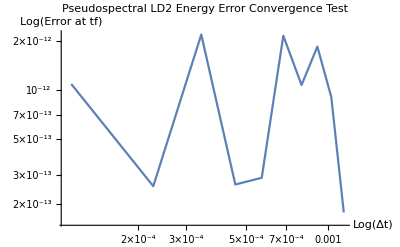

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorCN}], Joined->True,PlotLabel->"Pseudospectral LD2 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

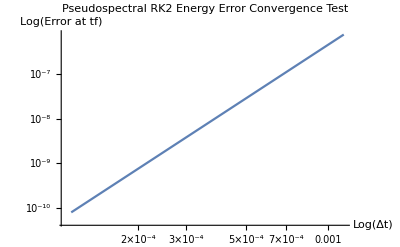

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorRK2}], Joined->True,PlotLabel->"Pseudospectral RK2 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

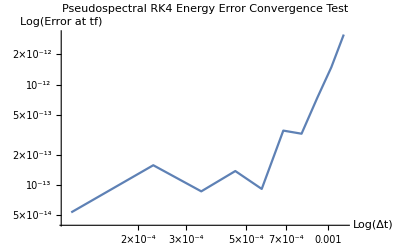

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorRK4}], Joined->True,PlotLabel->"Pseudospectral RK4 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```

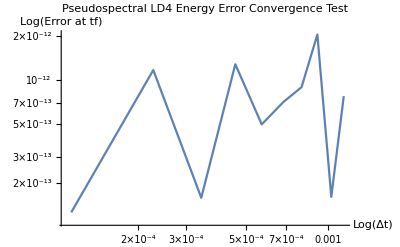

```mathematica
ListLogLogPlot[Transpose[{rs * deltax,PSfinalerrorLD4}], Joined->True,PlotLabel->"Pseudospectral LD4 Energy Error Convergence Test", AxesLabel->{"Log(Δt)","Log(Error at tf)"}]
```